```mathematica
Needs["Biomechanics`"]
```

Code written by Chris Richards, 
Royal Veterinary College, 2014
-- Package last Modified February 25, 2015, C. Richards

FOR HELP:
Type ?Function name

FOR SAMPLE CODE:
Type sampleBFilter[]
OR sampleDifferentiator[]

The functions in this package include:
BFilterR - forward-reverse (i.e. zero phase-shift) butterworth filter for smoothing 1d time series data
BFilter - butterworth filter for smoothing 1d time series data. 
Differentiator1D - Numerically differentiate 1d time series data
Integrator1D - Numerically integrate 1d time series data

```mathematica
(*initial posture and Ik snout position*)
range=0.1;
offset=1.57;
R={0.01,0.00802770,.02046710,.01779120,.0197439};
Manipulate[
(*afmj=-1.57;(*-0.5*)
af=-afmj+1.57;
at=-1.7;
aa=-1.4;(*-1.57*)
ak=3;(*3*)
ah=-3;(*-3*)*)
afmj=afmjSlider;
af=-afmj+1.57;
at=atSlider;
aa=aaSlider;
ak=akSlider;
ah=ahSlider;
p0={0,0};
p1=R[[1]]*{Cos[af],Sin[af]};
p2=p1+R[[2]]*{Cos[af+at],Sin[af+at]};
p3=p2+R[[3]]*{Cos[af+at+aa],Sin[af+at+aa]};
p4=p3+R[[4]]*{Cos[af+at+aa+ak],Sin[af+at+aa+ak]};
p5=p4+R[[5]]*{Cos[af+at+aa+ak+ah],Sin[af+at+aa+ak+ah]};
psnout=p5
ptarg={0.02,0.025};
Show[ListPlot[{p0,p1,p2,p3,p4,p5},PlotRange->{{-range,range},{-range,range}},AspectRatio->1,Joined->True],
ListPlot[{ptarg},PlotStyle->Orange]],
{{afmjSlider,-1.57},-Pi,Pi},{{atSlider,-1.65},-Pi,Pi},{{aaSlider,-1.5},-Pi,Pi},{{akSlider,3.14},-Pi,Pi},{{ahSlider,-3.12},-Pi,Pi}]
```

```mathematica
quat={Cos[(afmj)/2],0,Sin[(afmj)/2],0};
qposi=Flatten[{0,0,0,quat,{at,aa,ak,ah}}]
SetDirectory["/Users/chrisrichards/Desktop/FrogWork/Chris/CODE/MuJoCo/mjMOD_3SegRMdevel/RMsim"];
Export["qposInit.dat",{qposi}]
```

{0,0,0,0.707388,0,-0.706825,0,-1.65,-1.5,3.14,-3.12}

qposInit.dat

```mathematica
Accumulate[R]
```

{0.01,0.0180277,0.0384948,0.056286,0.0760299}

```mathematica
Clear[forcefun]
```

```mathematica
(*forces*)
forcefun[ampl_,phase_,period_,nsamples_]:=Table[
If[(phase>0)&&(t<phase),0,If[(phase<0)&&(t>(period+phase)),0,ampl*(0.5-0.5*Cos[2Pi*(t-phase)/period])]]

,{t,0,nsamples}]

actFun[ts_,dur_,s1_,s2_]:=Module[{wrise,wfall},
wrise=0.5+0.5*Tanh[2π*s1(2t-2ts)];
wfall=0.5-0.5*Tanh[2π*s2(2t-2(dur+ts))];
wrise*wfall
]

SetDirectory["/Users/chrisrichards/Desktop/FrogWork/Chris/CODE/MuJoCo/mjMOD_3SegRMdevel/RMsim"];
```

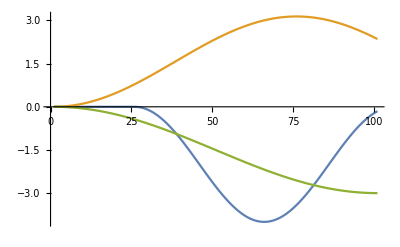

inforces.dat

```mathematica
stretch={0.8,1.5,2};
nsamples=100;
periods=nsamples*stretch;


forceA=forcefun[-4,25,periods[[1]],nsamples];
forceK=forcefun[3.14,0,periods[[2]],nsamples];
forceH=-forcefun[3,0,periods[[3]],nsamples];
ListLinePlot[{forceA,forceK,forceH}]
Export["inforces.dat",Transpose@{forceA,forceK,forceH}]
```

```mathematica
tf=0.15;
dt=0.001;
nsamples=tf/dt;
anklegain=0;
amps={-.5*anklegain,3,-3};
durs={0.05,0.5,0.2};
starts={0.02,0.01,0.01};
Manipulate[
ankFun=actFun[starts[[1]],durs[[1]],a1,a2];
kneFun=actFun[starts[[2]],durs[[2]],k1,k2];
hipFun=actFun[starts[[3]],durs[[3]],h1,h2];

forceA=Table[amps[[1]]*ankFun,{t,0,tf,(tf/(nsamples-1))}];
forceK=Table[amps[[2]]*kneFun,{t,0,tf,(tf/(nsamples-1))}];
forceH=Table[amps[[3]]*hipFun,{t,0,tf,(tf/(nsamples-1))}];

forceK=forceK-forceK[[1]];
forceH=forceH-forceH[[1]];

ListPlot[{forceA,forceK,forceH},PlotRange->All],{{a1,1.5},0.1,100},{{a2,3},0.1,100},{{k1,1.5},0.1,100},{{k2,3},0.1,100},{{h1,1.5},0.1,100},{{h2,3},0.1,100}]
```

```mathematica
Export["inforces.dat",Transpose@{forceA,forceK,forceH}]
```

inforces.dat

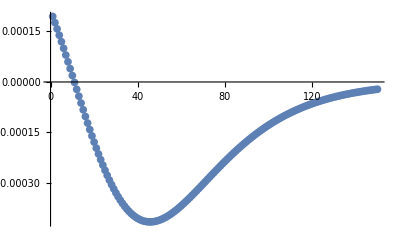

inforces.dat

```mathematica
dforceK=Differentiator1D[forceK,1,-1];
ddforceK=Differentiator1D[dforceK,1,-1];
ListPlot[ddforceK,PlotRange->All]
```

```mathematica
nsamples
```

200.

inforces.dat

```mathematica
forceA//Dimensions
```

{300}

```mathematica
//
```

```mathematica
nsamples
```

200.

```mathematica
(*---- NEED TO ADD ROLE OF FORELIMBS----*)
(*from Wang et al, 2014, forelimbs contribute roughly 1/2 BW of vertical force until*)
(*forelimb-off which is roughly at peak hindlimb GRF*)
;
;
;
```

0.0512878

```mathematica
(*------------RUN GET DATA FIRST!!!!!!-----------------------*)

writePoly[variableSymbol_,coefficientSymbols_]:=Module[{nterms,termList},
nterms=Length[coefficientSymbols];
termList=Table[coefficientSymbols[[i]]*variableSymbol^i,{i,2,nterms}];
termList=Join[{coefficientSymbols[[1]]},termList];
Total[termList]
]

actFun[ts_,dur_,s1_,s2_]:=Module[{wrise,wfall},
wrise=0.5+0.5*Tanh[2π*s1(2t-2ts)];
wfall=0.5-0.5*Tanh[2π*s2(2t-2(dur+ts))];
wrise*wfall
]

ankdur=0.05;
again=1;(*1*)
aAmp=-1;
Manipulate[

ankFun=actFun[astart,ankdur,a1,a2];


forceA=Table[aAmp*again*ankFun,{t,0,nsamples*dt,(nsamples*dt)/(nsamples-1)}];
ListPlot[forceA]
,{{astart,0.1},0.001,0.5},{{a1,1.5},0.1,10},{{a2,3},0.1,10}]
```

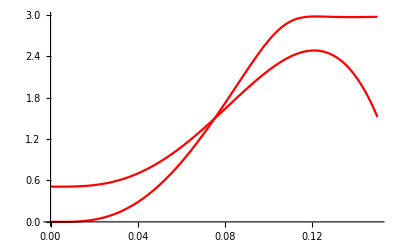

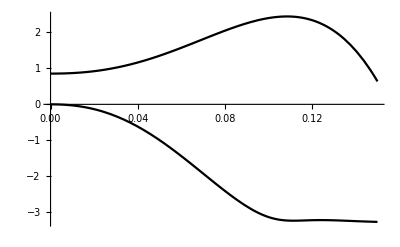

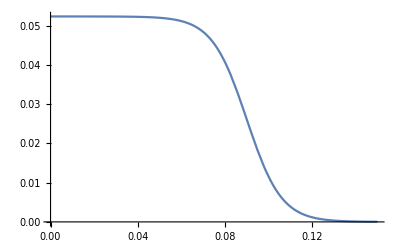

inforces.dat

```mathematica
kgain=1.5;
hgain=2;
nsamples=300;
dt=0.001;(*for mujoco sim*)

(*---forelimbs---*)
masses={0.000163,0.00015557,0.00036153,0.00077613,0.009};
mbody=Total[masses];
fforelimb=0.51*mbody*9.81;
rise=0.5+0.5*Tanh[2π*s1(2t-2ts)]/.{s1->5,ts->0.09};(*estimate time of peak force by peak hip/knee accel*)
forceFORE=fforelimb*(1-rise);
(*--------------*)


whichone=1;
polyOrder=4;
coefs=Table[ToExpression["a"<>ToString[i]],{i,1,polyOrder}];
rhs=writePoly[t,coefs];

trial=midJumps[[whichone]];
nframes=Length[pooledPOINTS[[trial]]];
akdata={};
ahdata={};
Do[
limb=pooledPOINTS[[trial,frame]];
vbod=limb[[6]]-limb[[5]];
vfem=limb[[4]]-limb[[5]];
vtib=limb[[4]]-limb[[3]];
ah=VectorAngle[limb[[6]]-limb[[5]],limb[[4]]-limb[[5]]];
ak=VectorAngle[limb[[3]]-limb[[4]],limb[[5]]-limb[[4]]];
akdata=Join[akdata,{{frame*videodt-videodt,ak}}];
ahdata=Join[ahdata,{{frame*videodt-videodt,ah}}];

,{frame,1,nframes}]

akfun=rhs/.FindFit[akdata,rhs,coefs,t];
ahfun=rhs/.FindFit[ahdata,rhs,coefs,t];

(*Show[
ListPlot[{akdata,ahdata},PlotStyle->{Red,Black}],
Plot[{akfun,ahfun},{t,0,nframes*videodt},PlotStyle->{Red,Black}]]*)


(*enforce to stay at final angle*)
wrise=0.5+0.5*Tanh[2π*s1(2t-2ts)]/.{s1->5,ts->0.11};
kfun=(1-wrise)*akfun+2.5*wrise;
hfun=(1-wrise)*ahfun+2.5*wrise;

kfun=kfun-(kfun/.t->0);
hfun=-(hfun-(hfun/.t->0));
kfun=kgain*kfun;
hfun=hgain*hfun;

(*(*base ankle force off of knee profile*)
afun=aAmp*again*D[(kfun-(kfun/.t->0)),t]/31/kgain;*)(*rougly 1 when again is 1*)


Plot[{kfun,akfun},{t,0,0.15},PlotRange->All,PlotStyle->Red]
Plot[{hfun,ahfun},{t,0,0.15},PlotRange->All,PlotStyle->Black]
(*Plot[afun,{t,0,0.15},PlotStyle->Blue]*)
Plot[forceFORE,{t,0,0.15}]


(*--resample--*)
(*forceA=Table[afun,{t,0,nsamples*dt,(nsamples*dt)/(nsamples-1)}];*)
forceK=Table[kfun,{t,0,nsamples*dt,(nsamples*dt)/(nsamples-1)}];
forceH=Table[hfun,{t,0,nsamples*dt,(nsamples*dt)/(nsamples-1)}];
forceFL=Table[forceFORE,{t,0,nsamples*dt,(nsamples*dt)/(nsamples-1)}];

(*--EXPORT---*)
SetDirectory["/Users/chrisrichards/Desktop/FrogWork/Chris/CODE/MuJoCo/mjMOD_3SegRMdevel/RMsim"];

Export["inforces.dat",Transpose@{forceA,forceK,forceH,forceFL}]
```

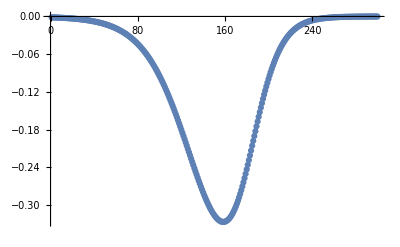

```mathematica
forceA//ListPlot
```